```mathematica
ClearAll["Global`*"]
```

```mathematica
table0331 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,33_1.txt",{"Table", "Data"}];
table0331[[All,1]]=table0331[[All,1]]-table0331[[1,1]];
table0331[[All,2]]=((table0331[[All,2]]+0.002)/(0.0043×0.05878));
table0331[[All,2]]=table0331[[All,2]]-Min[table0331[[All,2]]];
```

```mathematica
table0332 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,33_2.txt",{"Table", "Data"}];
table0332[[All,1]]=table0332[[All,1]]-table0332[[1,1]];
table0332[[All,2]]=((table0332[[All,2]]+0.002)/(0.0043×0.05878));
table0332[[All,2]]=table0332[[All,2]]-Min[table0332[[All,2]]];
```

```mathematica
table0333 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,33_3.txt",{"Table", "Data"}];
table0333[[All,1]]=table0333[[All,1]]-table0333[[1,1]];
table0333[[All,2]]=((table0333[[All,2]]+0.002)/(0.0043×0.05878));
table0333[[All,2]]=table0333[[All,2]]-Min[table0333[[All,2]]];
```

```mathematica
table0334 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,33_4.txt",{"Table", "Data"}];
table0334[[All,1]]=table0334[[All,1]]-table0334[[1,1]];
table0334[[All,2]]=((table0334[[All,2]]+0.002)/(0.0043×0.05878));
table0334[[All,2]]=table0334[[All,2]]-Min[table0334[[All,2]]];
```

```mathematica
table0335 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,33_5.txt",{"Table", "Data"}];
table0335[[All,1]]=table0335[[All,1]]-table0335[[1,1]];
table0335[[All,2]]=((table0335[[All,2]]+0.002)/(0.0043×0.05878));
table0335[[All,2]]=table0335[[All,2]]-Min[table0335[[All,2]]];
```

```mathematica
Export["table0331.dat",table0331];Export["table0332.dat",table0332];Export["table0333.dat",table0333];Export["table0334.dat",table0334];Export["table0335.dat",table0335];
```

```mathematica
T[k_,T0_,Tout_,t_]:=Tout+(T0-Tout)×Exp[-k×t]
```

```mathematica
fit0331=FindFit[table0331,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.577375,T0→43.617,Tout→-0.5439}

```mathematica
fit0332=FindFit[table0332,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.609189,T0→45.625,Tout→1.30741}

```mathematica
fit0333=FindFit[table0333,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.396401,T0→37.9871,Tout→-0.140352}

```mathematica
fit0334=FindFit[table0334,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.434744,T0→41.3265,Tout→1.16603}

```mathematica
fit0335=FindFit[table0335,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.344179,T0→45.9292,Tout→2.39403}

```mathematica
k0331=Mean[{k/.fit0331,k/.fit0332,k/.fit0333,k/.fit0334,k/.fit0335}]
```

0.472378

```mathematica
StandardDeviation[{k/.fit0331,k/.fit0332,k/.fit0333,k/.fit0334,k/.fit0335}]
```

0.115505

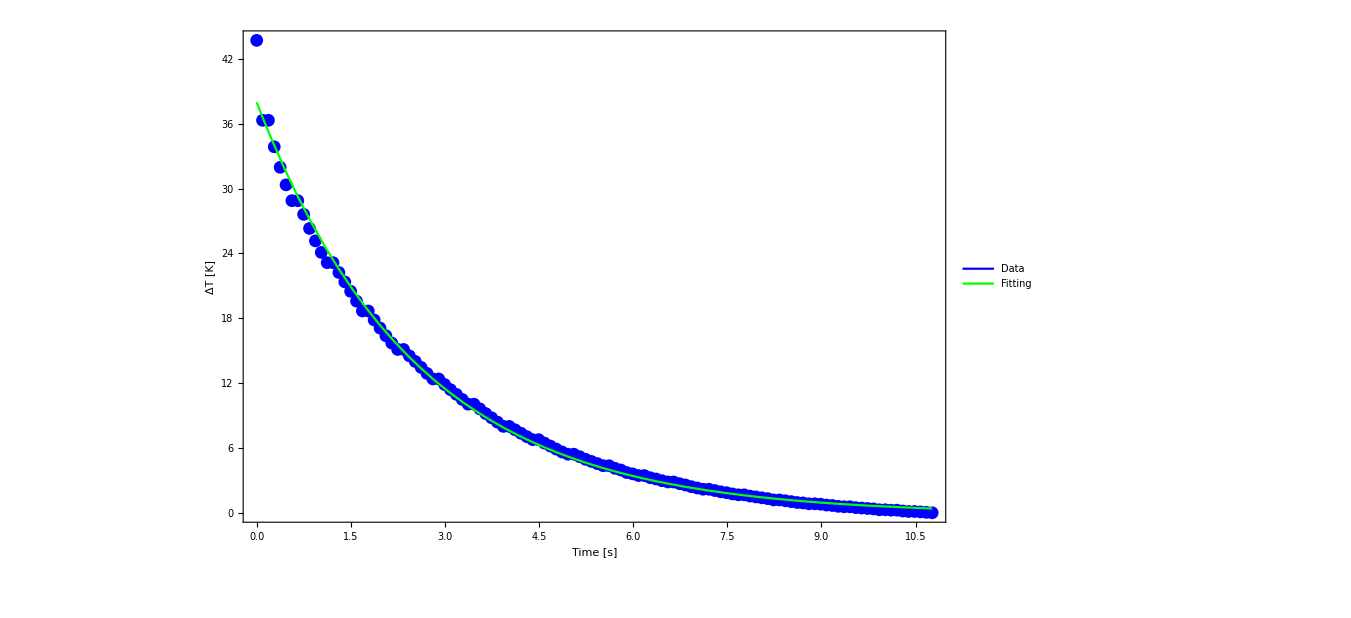

```mathematica
Legended[Show[ListPlot[table0333,PlotStyle->Blue],
Plot[T[k,T0,Tout,t]/.fit0333,{t,0,Max[table0333[[All,1]]]},PlotStyle->Green],  Frame->{True,True,False,False},FrameLabel->{"Time [s]","ΔT [K]"},ImageSize->1000, BaseStyle->{FontSize->24}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```